```mathematica
(** a = distance between two C atoms, b = lattice constant of triangular lattice **)
```

```mathematica
b=a Sqrt[3]
```

√3 a

```mathematica
a=1
```

1

```mathematica
PizzaSlice1=Polygon[{{0,0},{π/b,-π/(b Sqrt[3])},{4π/(3b),0},{π/b,π/(b Sqrt[3])}}];
```

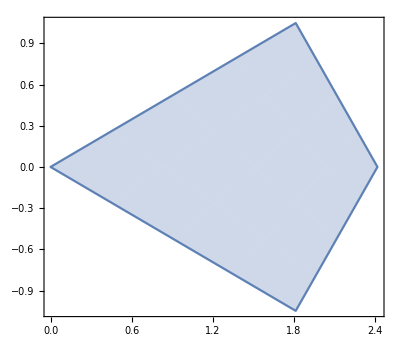

```mathematica
RegionPlot[PizzaSlice1,AspectRatio->Automatic]
```

```mathematica
PizzaSlice2=Polygon[{{0,0},{0,2π/(b Sqrt[3])},{-2π/(3b),2π/(b Sqrt[3])},{-π/b,π/(b Sqrt[3])}}];
```

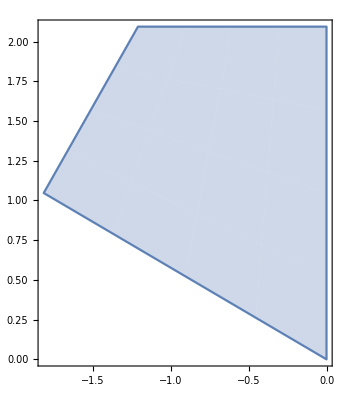

```mathematica
RegionPlot[PizzaSlice2,AspectRatio->Automatic]
```

```mathematica
PizzaSlice3=Polygon[{{0,0},{-π/b,-π/(b Sqrt[3])},{-2π/(3b),-2π/(Sqrt[3]b)},{0,-2π/(b Sqrt[3])}}];
```

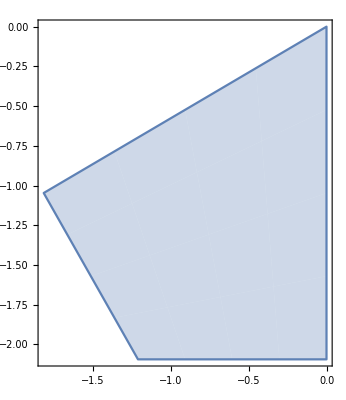

```mathematica
RegionPlot[PizzaSlice3,AspectRatio->Automatic]
```

```mathematica
PizzaSliceK=RegionUnion[PizzaSlice1,PizzaSlice2,PizzaSlice3];
```

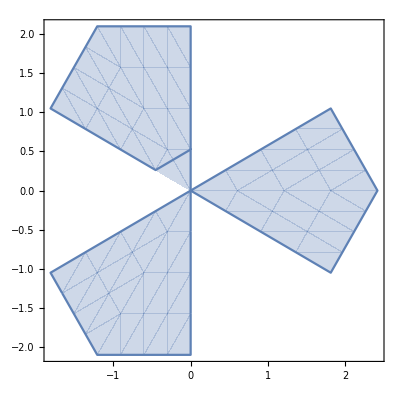

```mathematica
RegionPlot[PizzaSliceK,AspectRatio->Automatic]
```

```mathematica
BrillouinZone=Polygon[{{4π/(3b),0},{2π/(3b),2π/(Sqrt[3]b)},{-2π/(3b),2π/(Sqrt[3]b)},{-4π/(3b),0},{-2π/(3b),-2π/(Sqrt[3]b)},{2π/(3b),-2π/(Sqrt[3]b)}}];
```

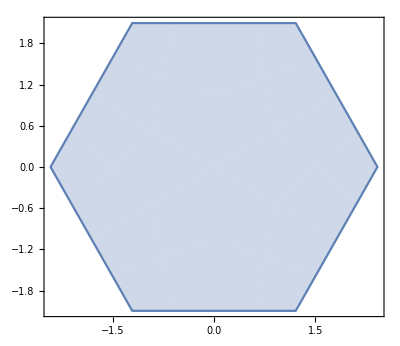

```mathematica
RegionPlot[BrillouinZone,AspectRatio->Automatic]
```

```mathematica
PizzaSliceKPrime=RegionDifference[BrillouinZone,PizzaSliceK];
```

```mathematica
RegionPlot[PizzaSliceKPrime, AspectRatio->Automatic]
```

-Graphics-

```mathematica
(** It finally turns out that Berry Connection does not depend on ϕ, the phase of the hopping amplitude **)
```

```mathematica
dVec[kx_,ky_,ϕ_,m_]:={Cos[ϕ]+Cos[b(kx/2 + Sqrt[3] ky/2 )+ ϕ]+Cos[b  kx+ ϕ],Sin[ϕ]+Sin[b(kx/2 + Sqrt[3] ky/2 )+ ϕ]+Sin[b  kx + ϕ],m}
```

```mathematica
dAmp[kx_,ky_,ϕ_,m_]:=Sqrt[Dot[dVec[kx,ky,ϕ,m],dVec[kx,ky,ϕ,m]]]
```

```mathematica
dCap[kx_,ky_,ϕ_,m_]:=dVec[kx,ky,ϕ,m]/dAmp[kx,ky,ϕ,m]
```

```mathematica
dCap[kx,ky,ϕ,m]
```

{(Cos[ϕ]+Cos[√3 kx+ϕ]+Cos[√3 (kx/2+(√3 ky)/2)+ϕ])/(√(m^2+(Cos[ϕ]+Cos[√3 kx+ϕ]+Cos[√3 (kx/2+(√3 ky)/2)+ϕ])^2+(Sin[ϕ]+Sin[√3 kx+ϕ]+Sin[√3 (kx/2+(√3 ky)/2)+ϕ])^2)),(Sin[ϕ]+Sin[√3 kx+ϕ]+Sin[√3 (kx/2+(√3 ky)/2)+ϕ])/(√(m^2+(Cos[ϕ]+Cos[√3 kx+ϕ]+Cos[√3 (kx/2+(√3 ky)/2)+ϕ])^2+(Sin[ϕ]+Sin[√3 kx+ϕ]+Sin[√3 (kx/2+(√3 ky)/2)+ϕ])^2)),m/(√(m^2+(Cos[ϕ]+Cos[√3 kx+ϕ]+Cos[√3 (kx/2+(√3 ky)/2)+ϕ])^2+(Sin[ϕ]+Sin[√3 kx+ϕ]+Sin[√3 (kx/2+(√3 ky)/2)+ϕ])^2))}

```mathematica
D[dCap[kx,ky,ϕ,m],kx]//FullSimplify
```

{-((√3 (2 (2 Cos[(√3 kx)/2-ϕ]+(3+m^2) Cos[(√3 kx)/2+ϕ]) Sin[(3 ky)/2]+(3 Cos[ϕ]+Cos[√3 kx+ϕ]) Sin[3 ky]-2 Sin[√3 kx-ϕ]+9 Sin[ϕ]+2 (7+m^2+6 Cos[√3 kx]) Cos[(3 ky)/2] Sin[(√3 kx)/2+ϕ]+11 Sin[√3 kx+ϕ]+4 m^2 Sin[√3 kx+ϕ]+Cos[3 ky] (3 Sin[ϕ]+Sin[√3 kx+ϕ])+2 Sin[2 √3 kx+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))),(√3 (5 Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+2 Cos[√3 kx-ϕ]+3 (3+Cos[3 ky]) Cos[ϕ]+(11+4 m^2) Cos[√3 kx+ϕ]+Cos[3 ky] Cos[√3 kx+ϕ]+2 Cos[(3 ky)/2] ((7+m^2) Cos[(√3 kx)/2+ϕ]+3 Cos[(3 √3 kx)/2+ϕ])+2 Cos[2 √3 kx+ϕ]-2 (3+m^2) Sin[(3 ky)/2] Sin[(√3 kx)/2+ϕ]-Sin[3 ky] (3 Sin[ϕ]+Sin[√3 kx+ϕ])))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2)),(√3 m (2 Cos[(√3 kx)/2]+Cos[(3 ky)/2]) Sin[(√3 kx)/2])/((3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))}

```mathematica
DXdCap[kx_,ky_,ϕ_,m_] := {-((√3 (2 (2 Cos[(√3 kx)/2-ϕ]+(3+m^2) Cos[(√3 kx)/2+ϕ]) Sin[(3 ky)/2]+(3 Cos[ϕ]+Cos[√3 kx+ϕ]) Sin[3 ky]-2 Sin[√3 kx-ϕ]+9 Sin[ϕ]+2 (7+m^2+6 Cos[√3 kx]) Cos[(3 ky)/2] Sin[(√3 kx)/2+ϕ]+11 Sin[√3 kx+ϕ]+4 m^2 Sin[√3 kx+ϕ]+Cos[3 ky] (3 Sin[ϕ]+Sin[√3 kx+ϕ])+2 Sin[2 √3 kx+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))),(√3 (5 Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+2 Cos[√3 kx-ϕ]+3 (3+Cos[3 ky]) Cos[ϕ]+(11+4 m^2) Cos[√3 kx+ϕ]+Cos[3 ky] Cos[√3 kx+ϕ]+2 Cos[(3 ky)/2] ((7+m^2) Cos[(√3 kx)/2+ϕ]+3 Cos[(3 √3 kx)/2+ϕ])+2 Cos[2 √3 kx+ϕ]-2 (3+m^2) Sin[(3 ky)/2] Sin[(√3 kx)/2+ϕ]-Sin[3 ky] (3 Sin[ϕ]+Sin[√3 kx+ϕ])))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2)),(√3 m (2 Cos[(√3 kx)/2]+Cos[(3 ky)/2]) Sin[(√3 kx)/2])/((3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))}
```

```mathematica
D[dCap[kx,ky,ϕ,m],ky]//FullSimplify
```

{-((3 (-Sin[1/2 (√3 kx-3 ky-2 ϕ)]-Sin[1/2 (√3 kx+3 ky-2 ϕ)]+3 Sin[ϕ]+3 Sin[√3 kx+ϕ]+2 Sin[(√3 kx)/2-(3 ky)/2+ϕ]+Sin[(3 √3 kx)/2-(3 ky)/2+ϕ]+2 (2+m^2) Sin[(√3 kx)/2+(3 ky)/2+ϕ]+Sin[(3 √3 kx)/2+(3 ky)/2+ϕ]+Sin[3 ky+ϕ]+Sin[√3 kx+3 ky+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))),(3 (Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+3 Cos[ϕ]+3 Cos[√3 kx+ϕ]+2 Cos[(√3 kx)/2-(3 ky)/2+ϕ]+Cos[(3 √3 kx)/2-(3 ky)/2+ϕ]+2 (2+m^2) Cos[(√3 kx)/2+(3 ky)/2+ϕ]+Cos[(3 √3 kx)/2+(3 ky)/2+ϕ]+Cos[3 ky+ϕ]+Cos[√3 kx+3 ky+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2)),(3 m Cos[(√3 kx)/2] Sin[(3 ky)/2])/((3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))}

```mathematica
DYdCap[kx_,ky_,ϕ_,m_] :={-((3 (-Sin[1/2 (√3 kx-3 ky-2 ϕ)]-Sin[1/2 (√3 kx+3 ky-2 ϕ)]+3 Sin[ϕ]+3 Sin[√3 kx+ϕ]+2 Sin[(√3 kx)/2-(3 ky)/2+ϕ]+Sin[(3 √3 kx)/2-(3 ky)/2+ϕ]+2 (2+m^2) Sin[(√3 kx)/2+(3 ky)/2+ϕ]+Sin[(3 √3 kx)/2+(3 ky)/2+ϕ]+Sin[3 ky+ϕ]+Sin[√3 kx+3 ky+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))),(3 (Cos[1/2 (√3 kx-3 ky-2 ϕ)]+Cos[1/2 (√3 kx+3 ky-2 ϕ)]+3 Cos[ϕ]+3 Cos[√3 kx+ϕ]+2 Cos[(√3 kx)/2-(3 ky)/2+ϕ]+Cos[(3 √3 kx)/2-(3 ky)/2+ϕ]+2 (2+m^2) Cos[(√3 kx)/2+(3 ky)/2+ϕ]+Cos[(3 √3 kx)/2+(3 ky)/2+ϕ]+Cos[3 ky+ϕ]+Cos[√3 kx+3 ky+ϕ]))/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2)),(3 m Cos[(√3 kx)/2] Sin[(3 ky)/2])/((3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))}
```

```mathematica
(1/2) Dot[dCap[kx,ky,ϕ,m],Cross[DXdCap[kx,ky,ϕ,m],DYdCap[kx,ky,ϕ,m]]]//FullSimplify
```

-(3 √3 m Sin[1/2 (√3 kx-3 ky)])/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))

```mathematica
BerryCurvature[kx_,ky_,ϕ_,m_]:=-(3 √3 m Sin[1/2 (√3 kx-3 ky)])/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))
```

```mathematica
-(3 √3 m Sin[1/2 (√3 kx-3 ky)])/(4 (3+m^2+2 Cos[√3 kx]+4 Cos[(√3 kx)/2] Cos[(3 ky)/2])^(3/2))//TeXForm
```

-\frac{3 \sqrt{3} m \sin \left(\frac{1}{2} \left(\sqrt{3} \text{kx}-3 \text{ky}\right)\right)}{4 \left(4 \cos \left(\frac{\sqrt{3}
   \text{kx}}{2}\right) \cos \left(\frac{3 \text{ky}}{2}\right)+2 \cos \left(\sqrt{3} \text{kx}\right)+m^2+3\right)^{3/2}}

```mathematica
Energy[kx_,ky_,ϕ_,m_]:=dAmp[kx,ky,ϕ,m]
```

```mathematica
Energy[kx,ky,0,m]
```

√(m^2+(1+Cos[√3 kx]+Cos[√3 (kx/2+(√3 ky)/2)])^2+(Sin[√3 kx]+Sin[√3 (kx/2+(√3 ky)/2)])^2)

```mathematica
en[kx_,ky_,m_]:=√(m^2+(1+Cos[√3 kx]+Cos[√3 (kx/2+(√3 ky)/2)])^2+(Sin[√3 kx]+Sin[√3 (kx/2+(√3 ky)/2)])^2)
```

```mathematica
Energy[4π/(3b),0,0,0]
```

0

```mathematica
Plot3D[{en[kx,ky,0],-en[kx,ky,0]},{kx,ky}∈BrillouinZone, BaseStyle->{FontFamily->"LatinModernRoman",FontSize->15},LabelStyle->Directive[Black,Bold,Medium],TicksStyle->Directive[Small,Blue], AxesLabel->{"k_y", "k_x","E_k"}]
```

-Graphics3D-

```mathematica
Plot3D[{en[kx,ky,0],-en[kx,ky,0]},{kx,-3,3},{ky,-3,3}, BaseStyle->{FontFamily->"LatinModernRoman",FontSize->15},LabelStyle->Directive[Black,Bold,Medium],TicksStyle->Directive[Small,Blue], AxesLabel->{"k_y", "k_x","E_k"}]
```

-Graphics3D-

```mathematica
Plot3D[BerryCurvature[kx,ky,0,0.001],{kx,ky}∈BrillouinZone,AxesLabel->{kx,ky},PlotStyle->Green,AxesLabel->{"k_y", "k_x","Ω"}]
```

-Graphics3D-

```mathematica
ChernNumberTotal[m_]:=NIntegrate[(1/(2π))BerryCurvature[kx,ky,0,m],{kx,ky}∈BrillouinZone,AccuracyGoal->8]//Chop
```

```mathematica
ChernNumberTotal[0.1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0

```mathematica
ChernNumberK1[m_]:=NIntegrate[(1/(2π))BerryCurvature[kx,ky,0,m],{kx,ky}∈PizzaSlice1]//Chop
```

```mathematica
ChernNumberK2[m_]:=NIntegrate[(1/(2π))BerryCurvature[kx,ky,0,m],{kx,ky}∈PizzaSlice2]//Chop
```

```mathematica
ChernNumberK3[m_]:=NIntegrate[(1/(2π))BerryCurvature[kx,ky,0,m],{kx,ky}∈PizzaSlice3]//Chop
```

```mathematica
A[m_]:={ChernNumberK1[m],ChernNumberK2[m],ChernNumberK3[m],ChernNumberK1[m]+ChernNumberK2[m]+ChernNumberK3[m]}
```

```mathematica
B[m_]:=NIntegrate[(1/(2π))BerryCurvature[kx,ky,0,m],{kx,ky}∈PizzaSliceK]//Chop
```

```mathematica
c=Table[{m,B[m]},{m,-2,2,0.1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{-2.,0.0852821},{-1.9,0.0917245},{-1.8,0.0988571},{-1.7,0.106772},{-1.6,0.115574},{-1.5,0.125384},{-1.4,0.13634},{-1.3,0.148596},{-1.2,0.162329},{-1.1,0.177732},{-1.,0.195014},{-0.9,0.214398},{-0.8,0.236105},{-0.7,0.260339},{-0.6,0.287265},{-0.5,0.316968},{-0.4,0.34942},{-0.3,0.384427},{-0.2,0.421608},{-0.1,0.460382},{0.,0},{0.1,-0.460382},{0.2,-0.421608},{0.3,-0.384427},{0.4,-0.34942},{0.5,-0.316968},{0.6,-0.287265},{0.7,-0.260339},{0.8,-0.236105},{0.9,-0.214398},{1.,-0.195014},{1.1,-0.177732},{1.2,-0.162329},{1.3,-0.148596},{1.4,-0.13634},{1.5,-0.125384},{1.6,-0.115574},{1.7,-0.106772},{1.8,-0.0988571},{1.9,-0.0917245},{2.,-0.0852821}}

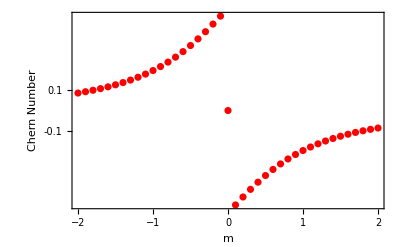

```mathematica
ListPlot[c,AxesLabel->{"m","Chern Number"},Frame-> True,FrameTicks->{{{-0.5,-0.3,-0.1,0,0.1,0.3,0.5},None},Automatic},PlotStyle->Red,FrameStyle-> Thick,FrameTicksStyle->{Black,14}]
```

```mathematica
d=Table[{m,B[m]},{m,-0.001,0.001,0.0001}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{-0.001,0.499602},{-0.0009,0.499642},{-0.0008,0.499682},{-0.0007,0.499722},{-0.0006,0.499761},{-0.0005,0.499801},{-0.0004,0.499841},{-0.0003,0.499881},{-0.0002,0.499921},{-0.0001,0.49996},{0.,0},{0.0001,-0.49996},{0.0002,-0.499921},{0.0003,-0.499881},{0.0004,-0.499841},{0.0005,-0.499801},{0.0006,-0.499761},{0.0007,-0.499722},{0.0008,-0.499682},{0.0009,-0.499642},{0.001,-0.499602}}

```mathematica
d1={{-0.001,0.49960237948002284},{-0.0009,0.4996421406233168},{-0.0008,0.4996819038789211},{-0.0007,0.4997216565626854},{-0.0006000000000000001,0.4997614106420638},{-0.0005,0.4998011812507986},{-0.00039999999999999996,0.4998409464353172},{-0.00030000000000000003,0.4998807105579699},{-0.00019999999999999998,0.49992052990301894},{-0.00009999999999999994,0.4999602559122733},{0.,0},{0.00010000000000000005,-0.49996025591227344},{0.0002000000000000001,-0.49992052990301894},{0.00030000000000000014,-0.4998807105579693},{0.00039999999999999996,-0.4998409464353172},{0.0005,-0.4998011812507986},{0.0006000000000000001,-0.4997614106420638},{0.0007000000000000001,-0.4997216565626854},{0.0008000000000000001,-0.4996819038789211},{0.0009,-0.4996421406233168},{0.001,-0.49960237948002284}}
```

{{-0.001,0.499602},{-0.0009,0.499642},{-0.0008,0.499682},{-0.0007,0.499722},{-0.0006,0.499761},{-0.0005,0.499801},{-0.0004,0.499841},{-0.0003,0.499881},{-0.0002,0.499921},{-0.0001,0.49996},{0.,0},{0.0001,-0.49996},{0.0002,-0.499921},{0.0003,-0.499881},{0.0004,-0.499841},{0.0005,-0.499801},{0.0006,-0.499761},{0.0007,-0.499722},{0.0008,-0.499682},{0.0009,-0.499642},{0.001,-0.499602}}

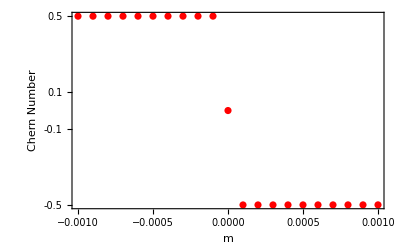

```mathematica
ListPlot[d,AxesLabel->{"m","Chern Number"},Frame->True,FrameTicks->{{{-0.5,-0.3,-0.1,0,0.1,0.3,0.5},None},Automatic},PlotStyle->Red,FrameStyle-> Thick,FrameTicksStyle->{Black,14}]
```

```mathematica
B[0.00001]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.499996

```mathematica
a=N[Table[{Log10[10^(-k)],Log10[B[10^(-k)]+0.5]},{k,1,5,0.5}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{-1.,-1.4021},{-1.5,-1.90069},{-2.,-2.40054},{-2.5,-2.90053},{-3.,-3.40053},{-3.5,-3.90052},{-4.,-4.40073},{-4.5,-4.90019},{-5.,-5.39047}}

```mathematica
lm=LinearModelFit[a,x,x]
```

FittedModel[-0.404357+0.99841 x]

```mathematica
10^lm[0]
```

0.394133

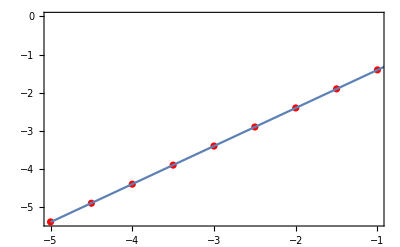

```mathematica
Show[ListPlot[a,PlotStyle->Red],Plot[lm[x],{x,-5,0}],Frame-> True]
```

```mathematica
(** In the limit of m -> 0, the Chern number of the two valleys are +/- 0.5, but at exact 0 it is 0 **)
```

```mathematica
(** Numerically, if we go beyond m ~ 10^-5, mathematica starts to give warning **)
```

```mathematica
(** Close to m ~ 0, the Chern number varies linearly with m **)
```